```mathematica
DSolve[{A'[t]==-A[t]/τa,B'[t]==A[t]/τa-B[t]/τb,B[0]==0},{A[t],B[t]},t]
```

{{A[t]→ⅇ^(-t/τa) C[1],B[t]→(ⅇ^(-t/τa-t/τb) (-ⅇ^(t/τa)+ⅇ^(t/τb)) τb C[1])/(τa-τb)}}

```mathematica
A[t_]:=ⅇ^(-t/τa)(1) 
B[t_]:=(ⅇ^(-t/τa-t/τb) (-ⅇ^(t/τa)+ⅇ^(t/τb)) τb(1))/(τa-τb)
τa=10;τb=5;
```

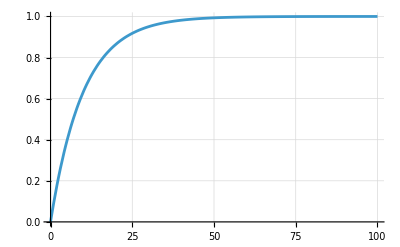

```mathematica
Plot[{B[t]/A[t]},{t,0,100},PlotRange->{{0,Automatic},{0,Automatic}},GridLines->Automatic]
```